## EWS plot for Fussmann system using Python data

## Import data

### EWS data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_fussmann_2000"];
```

```mathematica
(* data has form {deltaVals,varVals,cvVals,acVals,SmaxVals,aicFoldVals,aicHopfVals} *)
ewsChlorRaw=Import["data_export/ews_chlor.csv"];
ewsBrachRaw=Import["data_export/ews_brach.csv"];
```

### Bifurcation data

```mathematica
bifPtsChlor=Import["data/bifPtsChlor.mat"];
bifPtsBrach=Import["data/bifPtsBrach.mat"];
```

### General figure parameters

```mathematica
imgs=400;
aratio=0.25;
padding={{60,60},{20,20}};
{{padLeft,padRight},{padBottom,padTop}}=padding;
lt=0.006;
colChlor=Darker[TMBcolours[[1]],0.15];
colBrach=Darker[TMBcolours[[4]],0.15];
{colChlor,colBrach}
labelPos=Scaled[{0.04,0.85}];
```

{RGBColor[0.31315445, 0.43076214999999995, 0.6033283],RGBColor[0.7841471, 0.3277821, 0.17780215]}

## Bifurcation diagram

```mathematica
deltaVals=ewsChlorRaw[[2;;,1]]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

```mathematica
(* mark on approximate bifurcation points from experiment *)
expBif1a=deltaVals[[4]];
expBif1b=deltaVals[[5]];
expBif2=deltaVals[[9]];
expBifPts={expBif1a,expBif1b,expBif2};
```

```mathematica
(* chlorella bif *)
bifPlotChlorLines=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[lt]},{i,1,Length[bifPtsChlor]}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,4.2}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,4]*1000000,Range[0,4]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
ImagePadding->padding,
Epilog->{EdgeForm[Directive[Darker[Green,0.4],Thickness[0.003]]],Opacity[0.05],Directive[Darker[Green,0.4]],Rectangle[{expBif1a,0},{expBif1b,4200000}],Opacity[1],Line[{{expBif2,0},{expBif2,4200000}}],Directive[{Black}],
Line[Table[{Scaled[{0,-0.05},{deltaVals[[i]],0}],
Scaled[{0,0.05},{deltaVals[[i]],0}]},{i,1,Length[deltaVals]}]],
Directive[{Black}],Text[Style["a",14,Bold],Scaled[{0.04,0.9}]]}]
```

-Graphics-

```mathematica
bifPlotChlor=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[lt]},{i,1,Length[bifPtsChlor]}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,4.2}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,4]*1000000,Range[0,4]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
ImagePadding->padding,
Epilog->{Directive[{Black}],
Line[Table[{Scaled[{0,-0.05},{deltaVals[[i]],0}],
Scaled[{0,0.05},{deltaVals[[i]],0}]},{i,1,Length[deltaVals]}]],
Directive[{Black}],Text[Style["a",14,Bold],Scaled[{0.04,0.9}]]}]
```

-Graphics-

```mathematica
(* brachionus bif *)
bifPlotBrach=ListLinePlot[bifPtsBrach,
PlotRange->{{0,1.5},{-59/40,59}},
PlotStyle->Table[{colBrach,Thickness[lt]},{i,1,Length[bifPtsBrach]}],
LabelStyle->14,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlor. (10^6 cells/ml)",White],"Brach. (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
ImagePadding->padding];
```

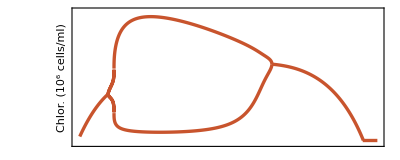
-Graphics--Graphics-

```mathematica
(* put together *)
bifPlot=Overlay[{bifPlotChlor,bifPlotBrach}]
```

## Plots of EWS against delta

### Variance

```mathematica
ewsChlorRaw[[1]]
```

{Delta,Variance,Coefficient of variation,Lag-1 AC,Lag-2 AC,Smax,AIC fold,AIC hopf,AIC null}

```mathematica
varChlor=ewsChlorRaw[[2;;,2]];
varBrach=ewsBrachRaw[[2;;,2]];
```

```mathematica
varPlotChlor=ListLinePlot[Transpose[{deltaVals,varChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Var(C)",""},{"",""}},
FrameTicks->{{Range[0,1,0.2],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",14,Bold],labelPos]}
];
```

```mathematica
varPlotBrach=ListLinePlot[Transpose[{deltaVals,varBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Var(B)"},{"",""}},
FrameTicks->{{None,Range[0,50,10]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

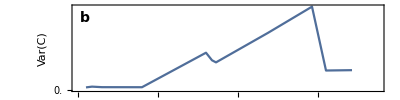
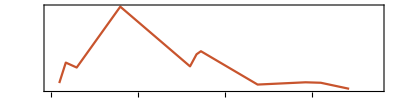

```mathematica
varPlot=Overlay[{varPlotChlor,varPlotBrach}]
```

### Coefficient of variation

```mathematica
cvarChlor=ewsChlorRaw[[2;;,3]];
cvarBrach=ewsBrachRaw[[2;;,3]];
```

```mathematica
cvarPlotChlor=ListLinePlot[Transpose[{deltaVals,cvarChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"C.V.(C)",""},{"",""}},
FrameTicks->{{Range[0,0.5,0.1],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}];
```

```mathematica
cvarPlotBrach=ListLinePlot[Transpose[{deltaVals,cvarBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","C.V.(B)"},{"",""}},
FrameTicks->{{None,Range[0,10,0.2]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

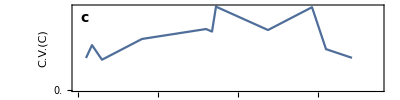
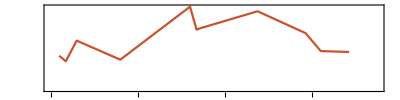

```mathematica
cvarPlot=Overlay[{cvarPlotChlor,cvarPlotBrach}]
```

### Lag-1 AC

```mathematica
acChlor=ewsChlorRaw[[2;;,4]];
acBrach=ewsBrachRaw[[2;;,4]];
```

```mathematica
acPlotChlor=ListLinePlot[Transpose[{deltaVals,acChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-1 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[Transpose[{deltaVals,acBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-1 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

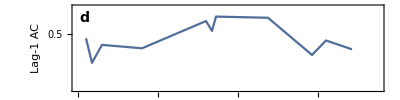
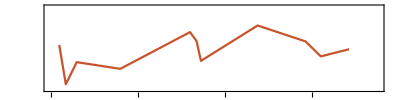

```mathematica
acPlot=Overlay[{acPlotChlor,acPlotBrach}]
```

### Lag-2 AC

```mathematica
acChlor=ewsChlorRaw[[2;;,5]];
acBrach=ewsBrachRaw[[2;;,5]];
```

```mathematica
acPlotChlor=ListLinePlot[Transpose[{deltaVals,acChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-2 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[Transpose[{deltaVals,acBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-2 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

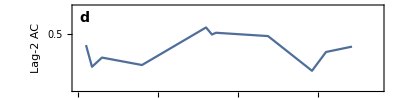
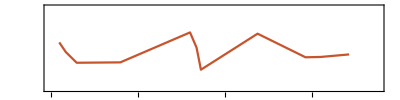

```mathematica
ac2Plot=Overlay[{acPlotChlor,acPlotBrach}]
```

### Smax

```mathematica
smaxChlor=ewsChlorRaw[[2;;,6]];
smaxBrach=ewsBrachRaw[[2;;,6]];
```

```mathematica
smaxPlotChlor=ListLinePlot[Transpose[{deltaVals,smaxChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"S_max(C)",""},{"",""}},
FrameTicks->{{Range[0,10,2]*10^(-2)//N,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["e",14,Bold],labelPos]}];
```

```mathematica
smaxPlotBrach=ListLinePlot[Transpose[{deltaVals,smaxBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","S_max(B)"},{"",""}},
FrameTicks->{{None,Range[0,10,1]//N},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

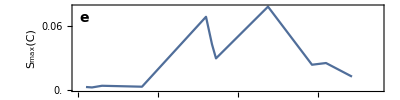
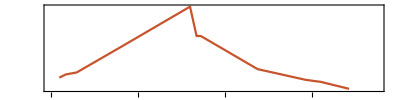

```mathematica
smaxPlot=Overlay[{smaxPlotChlor,smaxPlotBrach}]
```

### AIC weight fold

```mathematica
aicfoldChlor=ewsChlorRaw[[2;;,7]];
aicfoldBrach=ewsBrachRaw[[2;;,7]];
```

```mathematica
aicfoldPlotChlor=ListLinePlot[Transpose[{deltaVals,aicfoldChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_fold(C)",""},{"",""}},
FrameTicks->{{Range[0,1,0.2],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

```mathematica
aicfoldPlotBrach=ListLinePlot[Transpose[{deltaVals,aicfoldBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_fold(B)"},{"",""}},
FrameTicks->{{None,Range[0,1,0.2]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

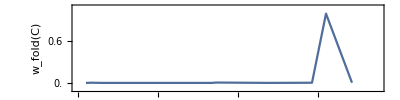
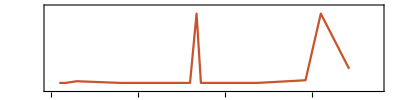

```mathematica
aicfoldPlot=Overlay[{aicfoldPlotChlor,aicfoldPlotBrach}]
```

### AIC weight hopf

```mathematica
aichopfChlor=ewsChlorRaw[[2;;,8]];
aichopfBrach=ewsBrachRaw[[2;;,8]];
```

```mathematica
aichopfPlotChlor=ListLinePlot[Transpose[{deltaVals,aichopfChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.3}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_hopf(C)",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*1.3,padTop}},
Epilog->{Directive[{Black}],Text[Style["f",14,Bold],labelPos]}];
```

```mathematica
aichopfPlotBrach=ListLinePlot[Transpose[{deltaVals,aichopfBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.3}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_hopf(B)"},{"Dilution rate δ (per day)",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*2.2,padTop}}];
```

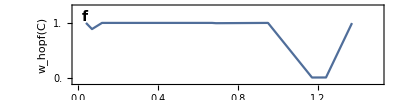
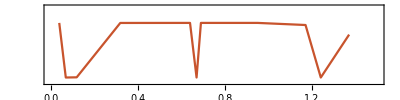

```mathematica
aichopfPlot=Overlay[{aichopfPlotChlor,aichopfPlotBrach}]
```

### AIC weight Null

```mathematica
aicNullChlor=ewsChlorRaw[[2;;,9]];
aicNullBrach=ewsBrachRaw[[2;;,9]];
```

```mathematica
aicNullPlotChlor=ListLinePlot[Transpose[{deltaVals,aicNullChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.2}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_null(C)",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*1.3,padTop}},
Epilog->{Directive[{Black}],Text[Style["f",14,Bold],labelPos]}];
```

```mathematica
aicNullPlotBrach=ListLinePlot[Transpose[{deltaVals,aicNullBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.2}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_null(B)"},{"Dilution rate δ (per day)",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*2.2,padTop}}];
```

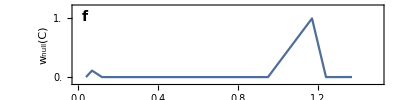
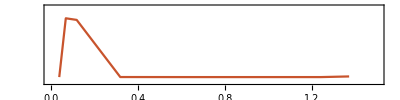

```mathematica
aicNullPlot=Overlay[{aicNullPlotChlor,aicNullPlotBrach}]
```

## Grid all plots together

```mathematica
ewsFussmannPlot=Grid[{{bifPlot},{varPlot},{cvarPlot},{acPlot},{smaxPlot},{aichopfPlot}},Spacings->{0,-1.5}]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Export["figures/ews_series.png",ewsFussmannPlot,ImageResolution->200];
```